# Math Autograder for Variety of Student Levels

Silas Grossberndt (Mentor: Robert Nachbar )

## -Graphics-

GOAL OF THE PROJECT: Today, with the rise of online courseware and self-learning, more and more students are being tested and graded by completely automated systems. This, unfortunately, has its drawbacks, as the questions are often multiple choice, allowing the student to rely on guessing, or require the entering of exact input, penalizing students for correct answers that are written in non-identical, but equivalent forms. One wants to create a system that can verify if the student has submitted an answer that is correct, not only checking for the answer, but instead checking equivalent forms. Each equivalence class must have an associated level, and derive its definition from those that may be garnered using mathematics taught by that point.

SUMMARY OF RESULTS: In this project I have:

1. Prepared and trained a Markov classifier that can read in a mathematics question in algebra 1, 2 or calculus, and establish which of the three it is with 93% accuracy.

2. Built and tested an engine containing all the necessary parts of a mathematics autograder on these subjects. 

3. Integrated these two together into a single application that provides a robust and scalable backend system to be implemented in a GUI.

ADDITIONAL CONTENT:

Training of the data:

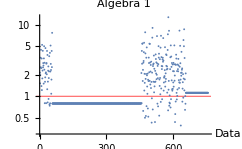
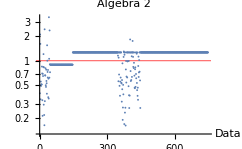
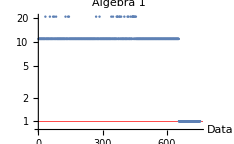
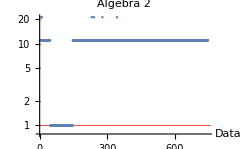
Method | Algebra1  | Algebra 2 | Accuracy
Automatic | -Graphics- | -Graphics- | 0.58
Markov | -Graphics- | -Graphics- | 0.93

Contextual Tags

Value | Meaning
0 | No Context Restrictions
1 | Simplest Form Fraction
2 | Decimal Representation
3 | A set of Points
4 | Calculus
5 | A set of Points of Simplest Fractions
6 | A set of Points in Decimal
7 | Mixed Number
8 | Improper Fraction

FUTURE WORK:  Further work could encompass the addition of further levels of question, the use of graphical data as a selected answer or the inclusion of a retraining function in the neural net to improve classification accuracy, as well as the integration of the data into two GUIs.  One has the student submits an answer to a randomly selected question from a database that has been built using Wolfram|Alpha's Problem Generator. The student may select one of the three levels, receive a question, submit an answer and check that it is correct. After the correct answer has been submitted, the system automatically pulls a new question from the list in the selected type. The second allows for the teacher to create a quiz and store it as a new database, which will then be fed to the first exemplar.